```mathematica
IntSincRotationMatrix[{a_,b_,T_}] := ({{T+(a^2 T (-1+Sinc[√(a^2+b^2) T]))/(a^2+b^2+ϵ), (a b T (-1+Sinc[√(a^2+b^2) T]))/(a^2+b^2+ϵ), 1/2 a T^2 Sinc[1/2 √(a^2+b^2) T]^2}, {(a b T (-1+Sinc[√(a^2+b^2) T]))/(a^2+b^2+ϵ), T+(b^2 T (-1+Sinc[√(a^2+b^2) T]))/(a^2+b^2+ϵ), 1/2 b T^2 Sinc[1/2 √(a^2+b^2) T]^2}, {-1/2 a T^2 Sinc[1/2 √(a^2+b^2) T]^2, -1/2 b T^2 Sinc[1/2 √(a^2+b^2) T]^2, T Sinc[√(a^2+b^2) T]}});  (* = (∫_0)^T exp W(t) dt = (∫_0)^T exp ({{0, 0, a t}, {0, 0, b t}, {-a t, -b t, 0}})dt *)
CylinderIIB[sx_,H_] := Module[{S,II,dN,d1,d2,iR,dns},
S = ({{sx, 0}, {0, 1}, {0, 0}}); (* constant in-plane deformation *)
(* compute normal derivatives *)
II = ({{H, 0}, {0, 0}});
dN = -Transpose[Inverse[S[[1;;2,1;;2]]]].II; (* under the assumption that n=001 we have S = (A; 0) and dN = (B; 0). then since S^T dN = II we have A^T B = II -> B = A^-T II *)
Print[dN];
d1={1,0}; (* principal curvature direction *)
d2={0,1}; (* orthogonal direction with 0 curvature *)
dns = dN.d1;
(* integrate rotation along principal direction *)
iR =  If[dN[[1,2]]== 0 && dN[[2,2]]==0 && False,{u,v}.d1 IdentityMatrix[3],IntSincRotationMatrix[{dns[[1]],dns[[2]],{u,v}.d1}]/.{ϵ->0}];
iR.(S.d1) + {0,v,0} (* sum of derivative integrated along curvature and orthogonal directions *)
];
ParametricPlot3D[Evaluate[CylinderIIB[1.1,1]],{u,-1,1},{v,-1,1}]
```

{{-0.909091,0.},{0.,0.}}

-Graphics3D-

```mathematica
Simplify[CylinderIIB[sx,H] // MatrixForm ,{sx,H}∈Reals]
```

{{-H/sx,0},{0,0}}

(sx u Sinc[(H u)/sx]
v
1/2 H u^2 Sinc[(H u)/(2 sx)]^2)

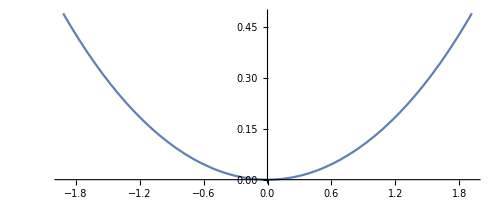

```mathematica
ParametricPlot[Flatten@({{sx u Sinc[(H u)/sx]}, {1/2 H u^2 Sinc[(H u)/(2 sx)]^2}})/.{sx->2,H->1},{u,-1,1}]
```